# The linearly non-separable feature-binding problem

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Code

### Init

```mathematica
$HistoryLength=100;
```

### compilation Attributes

```mathematica
Const/: (a_Symbol = Const[b_]) :=
(a =b; SetAttributes[a,Protected]; b)
```

```mathematica
SetAttributes[InlComp,HoldAll];
InlComp[inls_,parms_,code_,decl_] :=
Block[ {curprot,Trans2Rule,r1,r2,rcode,a,cmp,t},

curprot := Block[ {t,a,s} ,
t = Names[$Context<>"*"];
a = Map[Attributes,t];
t=t[[ Map[First,Position[a,Protected,{2}]] ]];t= Map[ToExpression[#,StandardForm,Hold]&,t]
];

SetAttributes[Trans2Rule,HoldAll];
    Trans2Rule[sym_] := Block[ {t},
t = DownValues[sym];
If [Length[t] == 0,
{HoldPattern[sym] -> sym},
t]
];

SetAttributes[cmp,HoldAll];

r1  = Apply[Trans2Rule,curprot,{1}];
r2 = Map[Trans2Rule,Unevaluated@inls];
rcode = Hold[code] //. Flatten[{r1,r2}];
t=cmp[parms,rcode,decl] /. HoldPattern[rcode]-> rcode /. Hold[a___] -> a;
Compile@@t
]
```

```mathematica
GlobalRefs[f_CompiledFunction]:= Block[ {a,b},
Cases[
f[[4]], 
HoldPattern[Function[a_List, b___]] -> HoldForm[b],
∞
]
]
```

## set values

```mathematica
NN=150;
 
(* input dimension *)
Tmax = Const[500+100];  (* max. inputlength *)
step = 0.2; 
Tonl=Const[Tmax-100];(* τM in paper (for the elgibility trace low pass filter) *)
w = Table[1,{NN}]; (* no weight!!! *)
Urest = Const[-1] ;(* resting potential *)
(*α : factor of reduction of s^ν and Subscript[E, i] over one time step *)
α=N[1-step/Tonl];
(*β : factor of reduction of Subscript[e, i] over one time step *)
β=N[step/Tonl];
γ=N[1/Tonl];
(*invE : threshold for s^ν *)
tmr = 10.0; (* decay time of the reset kernel *)
tmrini =N[ 10/tmr]; (* constant to update resets of spiking neurons *)
tmrsfac=N[1-step/tmr]; (* factor of reduction of the reset kernel over one time step *)
rewdelay = 0.;(*delay for a reward *)
FlucLen =0; (* to modulate the pattern length *)
λ=1; (* smoothing factor for the exponential moving average *)
tNMDA=50//Const;(*duration of a NMDA spike *)
stNMDA= IntegerPart[tNMDA/step]; (* number of steps for a NMDA spike *)
stNMDAReal=1.0*stNMDA;(* number of steps for a NMDA spike *)
UspikeNMDA=0.3;
mu=0.1;
pConnect=0.5;(* connectivity probability *)
β2=5.;
βN=5.;
Umax=10.0//Const (*for the dendritic branches*);
UmaxSoma=2.//Const (*for the soma until le first order approx is quite correct*);
sigma=1.4;
pOff=0.2;
nbNeuron=40;
τfracSp=4;
msNumber=-Log[$MachineEpsilon *100.];
```

```mathematica
τs=1.5;τm=10.0;
```

```mathematica
fh=40.;
fl=5.;
```

```mathematica
UrestSoma=-1.6;
```

```mathematica
cSpikeTime=Tonl/2;(* desired spike time *)
cSpikeTimeStep=cSpikeTime/step;(* desired spike time (number of step) *)
```

```mathematica
τfrac=0.5//Const (* fraction of time cte for the low pass filters *);
```

```mathematica
BoundSyn=1000;
```

```mathematica
k2=Const[0.006737946999085467];
```

```mathematica
LearnSpike=True;
```

```mathematica
aAMPA:=N[1./(2*nbNeuron)];
```

```mathematica
stepperlist=0;(* to keep the membrane potential in "stepper" *)
```

```mathematica
setStep[newStep_]:=(step=newStep;αg=N[1-step/Tonl];βg=N[step/Tonl];γg=N[1/Tonl];αl=N[1-step/tNMDA];βl=N[step/tNMDA];γl=N[1/tNMDA];tmrsfac=N[1-step/tmr];stNMDA= IntegerPart[tNMDA/step];stNMDAReal=1.0*stNMDA;);
```

```mathematica
βN=5.;
```

```mathematica
setStep[step];
```

## Develop functions

### load packages

```mathematica
(* to write in the Messages windows *)
msg[expr_] := NotebookWrite[First@Notebooks["Messages"],
Cell[BoxData[MakeBoxes[expr,StandardForm]],"Output"]];
```

### define getFileName

```mathematica
getFileName[lstep_,trials_, opt_]:="./out/"<>"_eta"<>ToString[lstep//N]<>"_trials"<>ToString[trials]<>"_IL"<>ToString[NN]<>"_NbNeurons"<>ToString[nbNeuron]<>"_USpike"<>ToString[UspikeNMDA]<>"_Patn"<>ToString[Patn]<>"_SigmaW"<>ToString[σW]<>"_UrS"<>ToString[UrestSoma]<>"_aAMPA"<>ToString[aAMPA]<>"_"<>opt<>".out"
```

### define postsynaptic and reset kernel

```mathematica
myeps[] := Block[ {tm = τm,ts=τs}, 
  (ⅇ^(-t/tm)-ⅇ^(-t/ts))/(tm-ts)]
```

```mathematica
myeta[]:= Block[ {tm = τm},
ⅇ^(-t/tm)/tm];
```

```mathematica
eps[t_] =myeps[];
SetAttributes[eps,Listable];
eta[t_] = 3myeta[];
SetAttributes[eta,Listable];
```

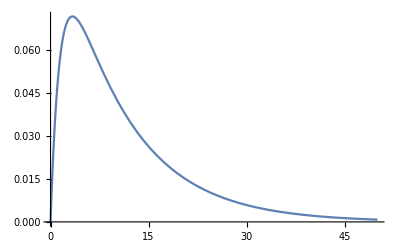

```mathematica
Plot[eps[t],{t,0,50}]
```

```mathematica
Integrate[eps[t],{t,0,∞}]
```

1.

### define stochastic intensity

```mathematica
(* escape noise for the dendrites *)
(*{ϕN,DϕN,DlϕN} = Block[ 
{k =100.(* firing at saturation *),β =5.0 (* Noise*),d =10000.0 (* shift factor*),dd,
f,df,dlf,u,kk,ββ ,a,b,c, cc},
f =  kk/(1+dd*Exp[-ββ*t]);
df =(kk*dd*ββ*Exp[-ββ*t])/(1+dd*Exp[-ββ*t])^2;
dlf = (ββ*dd)/(Exp[ββ*t]+dd);
{f,df,dlf} ={f,df,dlf}  /. {kk -> k,ββ ->  β,dd ->  d};
Map[ Function[ {t}, #]&, {a,b,c  +cc*t}]/. {a -> f, b-> df, c-> dlf,cc ->0.}
];*)
```

```mathematica
(* escape noise for the dendrites *)
{ϕN,DϕN,DlϕN} = Block[ 
{k =5.(* firing at saturation *),β =5.0 (* Noise*),d =1096.63 (* shift factor*),dd,
f,df,dlf,u,kk,ββ ,a,b,c, cc},
f =  kk/(1.0+dd*t);
df =(kk*dd*ββ*t)/(1.0+dd*t)^2;
dlf = (ββ*dd)/(1./t+dd);
{f,df,dlf} ={f,df,dlf}  /. {kk -> k,ββ ->  β,dd ->  d};
Map[ Function[ {t}, #]&, {a,b,c  +cc*t}]/. {a -> f, b-> df, c-> dlf,cc ->0.}
];
```

```mathematica
(* escape noise for the soma *)
{ϕS,DϕS,DlϕS} = Block[ 
{k =k2,β =β2,
f,df,dlf,u,kk,ββ ,a,b,c, cc},
f =  kk ⅇ^(ββ *t);
df =kk ββ ⅇ^(ββ *t);
dlf = (*df/f*)ββ;
{f,df,dlf} ={f,df,dlf}  /. {kk -> k,ββ ->  β};
Map[ Function[ {t}, #]&, {a,b,c  +cc*t}]/. {a -> f, b-> df, c-> dlf,cc ->0.}
];
```

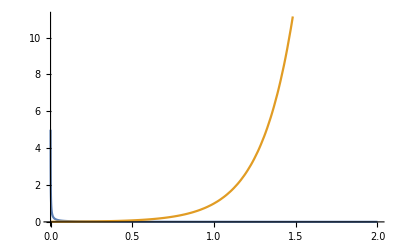

```mathematica
Plot[{ϕN[u],ϕS[u]},{u,0,2}]
```

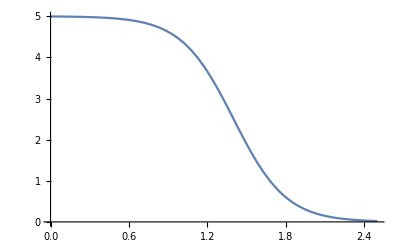

```mathematica
Plot[{DlϕN[Exp[-β2*u]]},{u,0,2.5}]
```

### define mempots

```mathematica
(* to calculate the membrane potential in the dendritic branchs *)
mempots[w_,inp_] := Block[ {tmp,us},
us=w.Transpose[inp]+Urest;
(*us= us* UnitStep[Umax-us]+Umax*UnitStep[us-Umax];*)(*saturation of the membrane potential at Umax *)
us
];
```

### define spikegenNMDA

```mathematica
(* spike or not with escape noise *)
spikegenNMDA[us_]:=
Block[{usf=Flatten[us],spikesi,t},
(*spikesi=Sign[step * ϕN[usf]-RandomReal[{0,1},Length[usf]]];*)
spikesi=Sign[1.-Exp[-step * ϕN[usf]]-RandomReal[{0,1},Length[usf]]];
If[Max[spikesi]≠1,{0},Flatten[Position[spikesi,1]]]
];
```

```mathematica
(* spike or not with escape noise *)
spikegenNMDA[us_,refPeriod_]:=
Block[{usf=Flatten[us],spikesi,t},
spikesi=Sign[step * ϕN[usf]*refPeriod-RandomReal[{0,1},Length[usf]]];If[Max[spikesi]≠1,{0},Flatten[Position[spikesi,1]]]
];
```

### define incrBuff

```mathematica
(* spike or not with escape noise *)
incrBuff[lindBuff_]:=
Block[{ind},
ind = Mod[lindBuff+1,stNMDA+1];
If[ind==0,1,ind]
];
```

### define myUnitStep

```mathematica
(Min[(tNMDA/(tNMDA+step)),Tonl/(Tonl+step)]+0.00001)/1000
```

0.000996026

```mathematica
myUnitStep[numb_]:=Block[{},
0.5*(Sign[(numb)+0.00099602593625498]+1.0)
];
```

### define ToFloat

```mathematica
ToFloat[numb_]:=Block[{numFl},
numFl=(numb*1.0);
numFl
];
```

### define SomaSat

```mathematica
SomaSat[u_]:=myUnitStep[UmaxSoma-u]u+myUnitStep[u-UmaxSoma]UmaxSoma;
```

### define spikegenPreSyn

```mathematica
(* spike or not with escape noise *)
spikegenPreSyn[rates_]:=
Block[{},
0.5*(Sign[1.-Exp[-(step/1000.(* rate in Hz and step in ms*)) * rates]-RandomReal[{0,1},Length[rates]]
]+1.)
];
```

### define stepper

```mathematica
stepper =
InlComp[
{mempots,spikegenNMDA,incrBuff,myUnitStep,ϕN,ϕS,k2,DϕN,DlϕN,DϕS,DlϕS,Tonl,step,stNMDA,tNMDA,β2,tmrsfac,αg,βg,γg,αl,βl,γl,τfrac,Urest,msNumber,UmaxSoma,SomaSat,τs,τm,spikegenPreSyn},
{{myinps,_Real,1},   (* input potentials *)
{myw,_Real,2},(* weights for the "dendritic neurons" and AMPA synapses for the first component*)
{resets,_Integer,1}, (* the NMDA spike response *)
{reset,_Real}, (* the reset kernel for the soma *)
{ETr,_Real,2}, (* the eligibility trace *)
{resets2,_Integer,1}, (* the NMDA spike response *)
{MemNMDASp,_Real,2}, (* memory of the synamtic state during the last NMDA spike *)
{BuffSyn,_Real,2} (* the no spiking part of Pfister ET over 50ms *)
},
Block[ {uSoma (*membrane potential at the soma *),ud, ntUpd,Updinc,thisinp,spikesNMDA,SpikeSoma,us,nw,i,len,istepperlist,mask,nmyresets,nmyreset,nBufUpd ,dendStructSpUpd,inRefPer,nUspikeNMDA,κ,ntAttIntSpikeNMDA,EligSoma,ntAttIntNMDA,intRefdendStruct,myET,indBuff=0,NMDASpikeCounts,nmBuffSyn,argFI,dendStruct,nmyinps,naAMPA,nτfracSp,nUrestSoma,ntmrini,FRS,PSPm,PSPs,spikesPre},

(*local compy to change of context only at the begining*)
ntmrini=tmrini;
nUrestSoma=UrestSoma;
nmyinps=myinps;
PSPm=0.0*nmyinps;
PSPs=0.0*nmyinps;
spikesPre=PSPs;
mask = Mask;
nUspikeNMDA=UspikeNMDA;
κ=N[k2*(Exp[β2*nUspikeNMDA]-1.)];
len =  Round[Tonl/step];
istepperlist = stepperlist;
myET=(*0.0**)ETr;
nw = myw;
naAMPA=aAMPA;
nτfracSp=τfracSp;
nmyresets =(*0**)resets (*Table[0,{Length@nw}]*);
NMDASpikeCounts=resets2 ;
intRefdendStruct= nmyresets*0-stNMDA;
inRefPer=Table[0.,{Length@nw}];
dendStruct=Table[{1.},{Length@nw}];
NMDASpikeCounts=resets;
dendStructSpUpd= nUspikeNMDA*β2+inRefPer;
EligSoma=inRefPer;
nmyreset=(*0.**)reset;
Updinc=0.0*nw;
ntUpd=Updinc;
ntAttIntSpikeNMDA=(*0.0**)MemNMDASp(*Updinc*);(* memory of the state of the synapses when a NMDA spike occurs*)
(*represent the 50ms low pass filter of the no spiking part of Pfister ET*)
(*nBufUpd = BuffSyn*)(* Table[ntUpd,{stNMDA}]*);(* buffer for e^iv *)
ntAttIntNMDA=(*0.0**)BuffSyn; 
uSoma=0.;
EligSoma=inRefPer;
argFI=dendStruct;
FRS=0.;

For[i=1, i≤len,i++,
(*indBuff=incrBuff[indBuff];*)
nmyresets = nmyresets+1; (* refractoriness period *)
NMDASpikeCounts = NMDASpikeCounts+1; (* refractoriness period *)
inRefPer=0.5(Sign[nmyresets-0.1] +1.) ;(* determine the sign of the  attenuation integral *)

(*Pre synaptic spikes *)
spikesPre=spikegenPreSyn[nmyinps];
PSPm=spikesPre+(1.0-step/τm)PSPm;
PSPs=spikesPre+(1.0-step/τs)PSPs;
thisinp ={(PSPm-PSPs)/(τm-τs)};   (* vector of inputs as a matrix *)

ud= mempots[nw,thisinp] ; (* calculate the membrane potential in the dendritic branchs ("line vector") *)
argFI=Exp[-β2*ud];
spikesNMDA= spikegenNMDA[argFI(*,inRefPer*)]; (* calculate the NMDA spikes *)
uSoma=nUspikeNMDA*Total[1.-inRefPer]-nmyreset+nUrestSoma+naAMPA*Total[Flatten@ud-Urest];
nmyreset = nmyreset  tmrsfac;
FRS=step * ϕS[SomaSat[uSoma]];
SpikeSoma=Sign[1.-Exp[-FRS]-RandomReal[{0,1}]];
(* somatic spike *)
If[SpikeSoma==1,
EligSoma=(*dendStructSpUpd*)Log[(1.-Exp[-FRS ⅇ^(nUspikeNMDA β2  inRefPer)])/(1.-Exp[-FRS ⅇ^(-nUspikeNMDA β2 (1.-inRefPer))])];
Updinc=(naAMPA* DlϕS[uSoma*dendStruct]FRS/(ⅇ^FRS-1.)).thisinp;
nmyreset+=ntmrini;
Sow[ i];,

EligSoma=-(step*κ)*Exp[β2*SomaSat[(uSoma-nUspikeNMDA)+nUspikeNMDA*inRefPer]];
Updinc=(-naAMPA*step*DϕS[SomaSat@uSoma*dendStruct]).thisinp;
];

ntUpd =Updinc+0.5 ntAttIntNMDA*EligSoma*inRefPer+0.5 ntAttIntSpikeNMDA*EligSoma*(1.0-inRefPer)(**(0.5(Sign[NMDASpikeCounts-0.1] +1.) )*);(*temrm without attenuation *)

(* calc of the eligibilite trace *)
Updinc =(step*DϕN[argFI]).thisinp;


(* NMDA spikes *)
If [spikesNMDA ≠ {0} ,(
NMDASpikeCounts[[spikesNMDA ]]=nmyresets[[spikesNMDA ]] ;
nmyresets[[spikesNMDA ]] = intRefdendStruct[[spikesNMDA ]];
Sow[ i,spikesNMDA];
us = argFI[[spikesNMDA]];
Updinc[[spikesNMDA]]=0.0*Updinc[[spikesNMDA]];
ntAttIntNMDA[[spikesNMDA]]=Updinc[[spikesNMDA]];
ntAttIntSpikeNMDA[[spikesNMDA]]=( DlϕN[us]).thisinp;
)];

(*myET=ntUpd+myET;*)
myET=ntUpd+(1.0-step/(τfrac*Tonl))myET;

If[(istepperlist==1 ),
Sow[{uSoma,ud,nUspikeNMDA*Total[1.-inRefPer],naAMPA*Total[Flatten@ud-Urest]},"ReturnValue"];
];

(*ntAttIntNMDA=ntAttIntNMDA-nBufUpd[[indBuff]];
nBufUpd[[indBuff]]=Updinc;
ntAttIntNMDA=ntAttIntNMDA+Updinc;*)
ntAttIntNMDA=Updinc+(1.0-step/(τfrac*tNMDA))*ntAttIntNMDA;
(*ntAttIntSpikeNMDA=(1.0-step/(τfrac*tNMDA))*ntAttIntSpikeNMDA;*)
];
Sow[{uSoma,ud,0.0,0.0},"ReturnValue"];
Sow[{nw,nmyresets,nmyreset,myET,NMDASpikeCounts,ntAttIntSpikeNMDA,ntAttIntNMDA},"ReturnValue"];
],
{{Mask,_Real,2},{UspikeNMDA,_Real},{UrestSoma,_Real},{aAMPA,_Real},{τfracSp,_Real},{stepperlist,_Integer},{Position[_, 1],_Integer,2}}
];
```

```mathematica
GlobalRefs[stepper]
```

{}

### define passEpisode

#### pass at the beginning (no resets, lags(=s^⋁), deriv(=E_i) yet)

```mathematica
passEpisode[w_, inps_] := passEpisode[inps,w,Table[0,{Length@w}],0.0,0.0*w,Table[0,{Length@w}],0.0*w,0.0*w];
```

#### pass later

```mathematica
passEpisode[inps_,w_,resets_,reset_,ET_,resets2_,memNMDASp_,memSyn_] := Block[ {resl,Y,Z},
{{resl,Y},Z}  =Reap[Reap[
Reap[stepper[inps, w,resets,reset,ET,resets2,memNMDASp,memSyn],"ReturnValue"][[2,1]] ,
 Range@First@Dimensions@w]];
{resl,({Y,Z} /. {{a__}} -> {a})}
];
```

#### nextpass later

```mathematica
nextpassEpisode[inps_,lresl_] := (
passEpisode[inps,Sequence@@lresl]);
```

#### nextpass at the beginning

```mathematica
nextpassEpisode[inps_,ww_ini (*to differentiate the 2 func nextpass *) ] :=  passEpisode[First@ww,inps];
(* only if the second argument (ww_) is of type ini  *)
```

### define passEpisodeEval

```mathematica
stepperEval =
InlComp[
{mempots,spikegenNMDA,incrBuff,myUnitStep,ϕN,ϕS,k2,DϕN,DlϕN,DϕS,DlϕS,Tonl,step,stNMDA,tNMDA,β2,tmrsfac,αg,βg,γg,αl,βl,γl,τfrac,Urest,msNumber,UmaxSoma,SomaSat,τs,τm,spikegenPreSyn},
{{myinps,_Real,1},   (* input potentials *)
{myw,_Real,2},(* weights for the "dendritic neurons" and AMPA synapses for the first component*)
{resets,_Integer,1}, (* the NMDA spike response *)
{reset,_Real}, (* the reset kernel for the soma *)
{ETr,_Real,2}, (* the eligibility trace *)
{resets2,_Integer,1}, (* the NMDA spike response *)
{MemNMDASp,_Real,2}, (* memory of the synamtic state during the last NMDA spike *)
{BuffSyn,_Real,2} (* the no spiking part of Pfister ET over 50ms *)
},
Block[ {uSoma (*membrane potential at the soma *),ud, ntUpd,Updinc,thisinp,spikesNMDA,SpikeSoma,us,nw,i,len,istepperlist,mask,nmyresets,nmyreset,nBufUpd ,dendStructSpUpd,inRefPer,nUspikeNMDA,κ,ntAttIntSpikeNMDA,EligSoma,ntAttIntNMDA,intRefdendStruct,myET,indBuff=0,NMDASpikeCounts,nmBuffSyn,argFI,dendStruct,nmyinps,naAMPA,nτfracSp,nUrestSoma,ntmrini,FRS,PSPm,PSPs,spikesPre},

(*local compy to change of context only at the begining*)
ntmrini=tmrini;
nUrestSoma=UrestSoma;
nmyinps=myinps;
PSPm=0.0*nmyinps;
PSPs=0.0*nmyinps;
spikesPre=PSPs;
mask = Mask;
nUspikeNMDA=UspikeNMDA;
κ=N[k2*(Exp[β2*nUspikeNMDA]-1.)];
len =  Round[Tonl/step];
istepperlist = stepperlist;
myET=(*0.0**)ETr;
nw = myw;
naAMPA=aAMPA;
nτfracSp=τfracSp;
nmyresets =(*0**)resets (*Table[0,{Length@nw}]*);
NMDASpikeCounts=resets2 ;
intRefdendStruct= nmyresets*0-stNMDA;
inRefPer=Table[0.,{Length@nw}];
dendStruct=Table[{1.},{Length@nw}];
NMDASpikeCounts=resets;
dendStructSpUpd= nUspikeNMDA*β2+inRefPer;
EligSoma=inRefPer;
nmyreset=(*0.**)reset;
Updinc=0.0*nw;
ntUpd=Updinc;
ntAttIntSpikeNMDA=(*0.0**)MemNMDASp(*Updinc*);(* memory of the state of the synapses when a NMDA spike occurs*)
(*represent the 50ms low pass filter of the no spiking part of Pfister ET*)
(*nBufUpd = BuffSyn*)(* Table[ntUpd,{stNMDA}]*);(* buffer for e^iv *)
ntAttIntNMDA=(*0.0**)BuffSyn; 
uSoma=0.;
EligSoma=inRefPer;
argFI=dendStruct;
FRS=0.;

For[i=1, i≤len,i++,
(*indBuff=incrBuff[indBuff];*)
nmyresets = nmyresets+1; (* refractoriness period *)
NMDASpikeCounts = NMDASpikeCounts+1; (* refractoriness period *)
inRefPer=0.5(Sign[nmyresets-0.1] +1.) ;(* determine the sign of the  attenuation integral *)

(*Pre synaptic spikes *)
spikesPre=spikegenPreSyn[nmyinps];
PSPm=spikesPre+(1.0-step/τm)PSPm;
PSPs=spikesPre+(1.0-step/τs)PSPs;
thisinp ={(PSPm-PSPs)/(τm-τs)};   (* vector of inputs as a matrix *)

ud= mempots[nw,thisinp] ; (* calculate the membrane potential in the dendritic branchs ("line vector") *)
argFI=Exp[-β2*ud];
spikesNMDA= spikegenNMDA[argFI(*,inRefPer*)]; (* calculate the NMDA spikes *)
uSoma=nUspikeNMDA*Total[1.-inRefPer]-nmyreset+nUrestSoma+naAMPA*Total[Flatten@ud-Urest];
nmyreset = nmyreset  tmrsfac;
FRS=step * ϕS[SomaSat[uSoma]];
SpikeSoma=Sign[1.-Exp[-FRS]-RandomReal[{0,1}]];
(* somatic spike *)
If[SpikeSoma==1,
nmyreset+=ntmrini;
Sow[ i];
];
(* NMDA spikes *)
If [spikesNMDA ≠ {0} ,(
NMDASpikeCounts[[spikesNMDA ]]=nmyresets[[spikesNMDA ]] ;
nmyresets[[spikesNMDA ]] = intRefdendStruct[[spikesNMDA ]];
Sow[ i,spikesNMDA];
)];

If[(istepperlist==1 ),
Sow[{uSoma,ud,nUspikeNMDA*Total[1.-inRefPer],naAMPA*Total[Flatten@ud-Urest]},"ReturnValue"];
];

];
Sow[{uSoma,ud,0.0,0.0},"ReturnValue"];
Sow[{nw,nmyresets,nmyreset,myET,NMDASpikeCounts,ntAttIntSpikeNMDA,ntAttIntNMDA},"ReturnValue"];
],
{{Mask,_Real,2},{UspikeNMDA,_Real},{UrestSoma,_Real},{aAMPA,_Real},{τfracSp,_Real},{stepperlist,_Integer},{Position[_, 1],_Integer,2}}
];
```

#### pass at the beginning (no resets, lags(=s^⋁), deriv(=E_i) yet)

```mathematica
passEpisodeEval[w_, inps_] := passEpisodeEval[inps,w,Table[0,{Length@w}],0.0,0.0*w,Table[0,{Length@w}],0.0*w,0.0*w];
```

#### pass later

```mathematica
passEpisodeEval[inps_,w_,resets_,reset_,ET_,resets2_,memNMDASp_,memSyn_] := Block[ {resl,Y,Z},
{{resl,Y},Z}  =Reap[Reap[
Reap[stepperEval[inps, w,resets,reset,ET,resets2,memNMDASp,memSyn],"ReturnValue"][[2,1]] ,
 Range@First@Dimensions@w]];
{resl,({Y,Z} /. {{a__}} -> {a})}
];
```

#### nextpass later

```mathematica
nextpassEpisodeEval[inps_,lresl_] := (
passEpisodeEval[inps,Sequence@@lresl]);
```

#### nextpass at the beginning

```mathematica
nextpassEpisodeEval[inps_,ww_ini (*to differentiate the 2 func nextpass *) ] :=  passEpisodeEval[First@ww,inps];
(* only if the second argument (ww_) is of type ini  *)
```

### define iniws (initial weights and Mask)

```mathematica
iniws[w_,num_,keepratio_]:=Block[{tmp,Mask},tmp=Norm[w,1]/Length[w];tmp=Table[w,{num}]+RandomReal[NormalDistribution[0,tmp],{num,Length[w]}];Mask=RandomReal[{0,1},{num,Length[w]}];
Mask=UnitStep[Mask-(1-keepratio)] 1.;
{tmp Mask,Mask}
]
```

### Def. functions to create patterns

```mathematica
Patn=4; (* number of patterns *)
Pats=Table[Xin[],{Patn}];
```

```mathematica
FlucLen=0;
MakePats[]:=(Pats=Table[Xin[Mod[k+1,2]],{k,4}];
PatLen=Table[1+Round[1/step(Tonl+2 FlucLen (Tmax-Tonl) (RandomReal[]-0.5))],{2},{2}];)
```

```mathematica
getActAff[affN_,satePatn_]:=If[affN≤NN/4,satePatn*fh+(1-satePatn)fl,satePatn*fl+(1-satePatn)fh]
```

```mathematica
Patsepsps0[x1_,x2_] := Table[If[l≤NN/2,getActAff[l,x1],getActAff[Mod[l,NN/2+1]+1,x2]]
,{l,NN}]
Clear[Patsepsps]; 
Patsepsps[x1_,x2_]:=Patsepsps[x1,x2]=Patsepsps0[x1,x2];(* patters as potentials *)
```

```mathematica
MakePats[]
```

### define myiniws

```mathematica
myiniws[μw_,σw_,num_,keepratio_]:=Block[{tmp,Mask},tmp=Table[μw,{num},{NN}];If[σw≠0,tmp+=RandomReal[NormalDistribution[0,σw],{num,NN}]];
Mask=RandomReal[{0,1},{num,NN}];
Mask=UnitStep[Mask-(1-keepratio)] 1.;
{tmp Mask,Mask}
]
```

### define getXid

```mathematica
getXid[num_ ]:=Block[{},
Which[num==1,{0,0},
num==2,{1,0},
num==3,{0,1},
num==4,{1,1}]
]
```

### define learn

```mathematica
rewdelay=0.;
learnEpisodes[wwin_,trials_,lstep_]:=Block[{last,ensrew=0,ww,x1,x2,c,o,nw,thisstep,dw,dwl,wl,cutoff,Rew,rewb,rews,resets,Z,Y,temp,t,n},
last=ini[wwin];
rewb=(R[#1,50+rewdelay,rewdelay,0.1]&)/@Itimes-1;
λ =0.2;
For[i=1,i≤trials,i++,
n=RandomInteger[{1,4}];
{x1,x2}=getXid[ n];(* choose ramndom pattern *)
{last,{Y,Z}}=nextpassEpisode[Patsepsps[x1,x2],last];
last=Last@last;(*we don't care about membrane pot*)
t=Mod[x1+x2,2];
Rew=-1. Abs[t-UnitStep[Length@Z-0.1]];

(*temp=o;*)
o=last[[4]]* Mask;

last[[1]]=last[[1]]+ lstep *Rew*(last[[4]]* Mask);(* weight update *)
temp=UnitStep[BoundSyn-Abs[last[[1]]]];
last[[1]]=temp*last[[1]]+(1.-temp)*BoundSyn;(* only weights smaller BoundSyn *)

ensrew=(1-λ) ensrew+λ (Rew);(* performance percentage as running mean *)(*If[Mod[i-1,10]==0,msg[{i,n,t,ensfield,o,Length[Patsepsps[n]]}]];*)
Sow[{Rew,Length@Z,Map[Length,Y],Norm[o],n},ensemble];
(*msg[Z];*)
];
First@last
];
```

```mathematica
(*give the Mean of the Initial Weights s.t. 80% of the synapses are exitatory*)
getMeanInitWeights[σ_,pOff_] := √2*σ*InverseErf[1-2.*pOff];
```

### define learnInFile

```mathematica
learnInFile[trials1_,trials2_,lstep_,opt_]:=Block[{tmp,tmp2,res,wwin,tmpSeed},
tmpSeed=IntegerPart[AbsoluteTime[]];
SeedRandom[tmpSeed];
Print["seed="<>ToString@tmpSeed];
{wwin,Mask} = myiniws[0.,σW,nbNeuron,0.5];
Patn=4;
Clear[Patsepsps];
Patsepsps[x1_,x2_]:=Patsepsps[x1,x2]=Patsepsps0[x1,x2];
MakePats[];

tmp=Reap[learnEpisodes[wwin,trials1,lstep],ensemble];
res=trialDT[outDT[Transpose[tmp[[2,1]]][[1]](* Perf *)],
outDT[Transpose[tmp[[2,1]]][[2]](* Z *)],
outDT[Transpose[tmp[[2,1]]][[3]](* Y *)],
outDT[Transpose[tmp[[2,1]]][[4]](* |Δw| *)],
outDT[tmp[[1]](* w *)],
outDT[tmpSeed],
outDT[Transpose[tmp[[2,1]]][[5]](* n *)]];
PutAppend[res,(getFileName[lstep,trials1, opt])];
If[trials2>0,
tmp2=Reap[learnEpisodes[tmp[[1]],trials2,lstep],ensemble];
res=trialDT[outDT[Join[Transpose[tmp[[2,1]]][[1]],Transpose[tmp2[[2,1]]][[1]]](* Perf *)],
outDT[Join[Transpose[tmp[[2,1]]][[2]],Transpose[tmp2[[2,1]]][[2]]](* Z *)],
outDT[Join[Transpose[tmp[[2,1]]][[3]],Transpose[tmp2[[2,1]]][[3]]](* Y *)],
outDT[Join[Transpose[tmp[[2,1]]][[4]],Transpose[tmp2[[2,1]]][[4]]](* |Δw| *)],
outDT[tmp2[[1]]],
outDT[tmpSeed],
outDT[Join[Transpose[tmp[[2,1]]][[5]],Transpose[tmp2[[2,1]]][[5]]]]
];
PutAppend[res,(getFileName[lstep,trials1+trials2, opt])];
];
];
```

### define ContlearnInFile

```mathematica
ContlearnInFile[trials1_,trials2_,lstep_,opt_]:=Block[{tmp,tmp2,res,wwin,Seedtab,WTab,k,PerfTab,ZTab,YTab,ΔwTab,ntab},
res=ReadList[getFileName[lstep,trials1, opt]];

PerfTab=res/.trialDT[outDT[a_],_,_,_,_,_,_]->a;
ZTab=res/.trialDT[_,outDT[a_],_,_,_,_,_]->a;
YTab=res/.trialDT[_,_,outDT[a_],_,_,_,_]->a;
ΔwTab=res/.trialDT[_,_,_,outDT[a_],_,_,_]->a;
WTab=res/.trialDT[_,_,_,_,outDT[a_],_,_]->a;
Seedtab=res/.trialDT[_,_,_,_,_,outDT[a_],_]->a;
ntab=res/.trialDT[_,_,_,_,_,_,outDT[a_]]->a;

For[k=1,k≤Length@WTab,k++,
SeedRandom[Seedtab[[k]]];
{wwin,Mask} = myiniws[0.,σW,nbNeuron,0.5];
Patn=4;
Clear[Patsepsps];
Patsepsps[x1_,x2_]:=Patsepsps[x1,x2]=Patsepsps0[x1,x2];
MakePats[];

Print@Timing[tmp2=Reap[learnEpisodes[WTab[[k]],trials2,lstep],ensemble];];
res=trialDT[outDT[Join[PerfTab[[k]],Transpose[tmp2[[2,1]]][[1]]](* Perf *)],
outDT[Join[ZTab[[k]],Transpose[tmp2[[2,1]]][[2]]](* Z *)],
outDT[Join[YTab[[k]],Transpose[tmp2[[2,1]]][[3]]](* Y *)],
outDT[Join[ΔwTab[[k]],Transpose[tmp2[[2,1]]][[4]]](* |Δw| *)],
outDT[tmp2[[1]]],
outDT[Seedtab[[k]]],
outDT[Join[ntab[[k]],Transpose[tmp2[[2,1]]][[5]]](* n *)]
];
PutAppend[res,(getFileName[lstep,trials1+trials2, opt])];
];
];
```

### λFilter

```mathematica
(*exp. moving average *)
 λFilter[incs_,λ_] := Block[ {fm},
fm[s_,inc_] := (1-λ)s + λ inc; 
FoldList[fm,0.5,incs]//Rest
];
```

## Plot functions

```mathematica
Needs["PlotLegends`"]
```

General::obspkg: "PlotLegends`" is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
Needs["ErrorBarPlots`"]
```

### define PlotPerfInFile

```mathematica
PlotPerfInFile[trials_,lstep_,opt_]:=Block[{tmp,res},
res=1.+ReadList[getFileName[lstep,trials, opt]]/.trialDT[outDT[a_],_,_,_,_,_,_]->a;
ListLinePlot[ λFilter[Mean@res,0.2/Patn],FrameLabel->{"trials","Perf"},
PlotLabel->"η="<>ToString[lstep]<>"  Patn="<>ToString[Patn]<>"  Runs="<>ToString[Length@res],
Frame->True,PlotRange->{0,1}]
];
```

```mathematica
PlotPerfInFile[names_,legends_]:=Block[{tmp,res},
res=Table[
λFilter[Mean[1+ReadList[n]/.trialDT[outDT[a_],_,_,_,_,_,_]->a],0.1/Patn],
{n,names}];
ListLinePlot[ res,FrameLabel->{"trials","Perf"},
PlotLegend->legends,LegendPosition->{1,-0.2}, LegendShadow->None,
Frame->True,PlotRange->{0,1}]
];
```

### define PlotWeightsInFile

```mathematica
PlotWeightsInFile[trials_,lstep_,opt_]:=Block[{tmp,res},
res=ReadList[getFileName[lstep,trials, opt]]/.trialDT[_,_,_,_,outDT[a_],_,_]->a;
res=Select[Flatten@res,(#≠0.0) &];
Histogram[res,Automatic(*{2}*),"Probability",PlotRange->All,AxesLabel->{"W","P(W)"},
PlotLabel->Style[Framed["μ="<>ToString[Mean@res]<>";    σ="<>ToString[StandardDeviation@res]],16]]
];
```

### define PlotWEvolInFile

```mathematica
PlotWEvolInFile[trials_,lstep_,opt_,lambda_,triaShow_]:=Block[{tmp,res},
res=ReadList[getFileName[lstep,trials, opt]]/.trialDT[_,_,_,outDT[a_],_,_,_]->a;
res=Map[Take[#,triaShow]&,res];
ListLinePlot[ λFilter[Mean@res,lambda],PlotRange->All,FrameLabel->{"trials","|W|"},
PlotLabel->"η="<>ToString[lstep]<>"  Patn="<>ToString[Patn],
Frame->True,PlotRange->{0,1}]
];
```

```mathematica
PlotWEvolInFile[trials_,lstep_,opt_,lambda_]:=Block[{tmp,res},
PlotWEvolInFile[trials,lstep,opt,lambda,trials]
];
```

```mathematica
PlotWEvolInFileList[trials_,lstep_,opt_]:=Block[{tmp,res},
res=ReadList[getFileName[lstep,trials, opt]]/.trialDT[_,_,_,outDT[a_],_,_,_]->a;
ListAnimate[Table[
ListLinePlot[ λFilter[res[[n]],1],PlotRange->All,FrameLabel->{"trials","|W|"},
PlotLabel->"η="<>ToString[lstep]<>"  Patn="<>ToString[Patn]<>"  Run="<>ToString[n],
Frame->True,PlotRange->{0,1}]
,{n,1,Length@res}]]
];
```

### define PlotMeanSomSpikeInFile

```mathematica
PlotMeanSomSpikeInFile[trials_,lstep_,opt_]:=Block[{tmp,res},
res=ReadList[getFileName[lstep,trials, opt]]/.trialDT[_,outDT[a_],_,_,_,_,_]->a;
res=Map[Length,res,{2}];
ListLinePlot[ λFilter[Mean@res,0.2/Patn],PlotRange->All,FrameLabel->{"trials","<|Z|>"},
PlotLabel->"η="<>ToString[lstep]<>"  Patn="<>ToString[Patn]<>"  Runs="<>ToString[Length@res],
Frame->True,PlotRange->{0,1}]
];
```

### define PlotMeanBranchSpikeInFile

```mathematica
PlotMeanBranchSpikeInFile[trials_,lstep_,opt_]:=Block[{tmp,res},
res=ReadList[getFileName[lstep,trials, opt]]/.trialDT[_,_,outDT[a_],_,_,_,_]->a;
res=Map[Length,res,{3}];
res=Map[Mean,res,{2}];
ListLinePlot[ λFilter[Mean@res,0.2/Patn],PlotRange->All,FrameLabel->{"trials","<|Y|>"},
PlotLabel->"η="<>ToString[lstep]<>"  Patn="<>ToString[Patn]<>"  Runs="<>ToString[Length@res],
Frame->True,PlotRange->{0,1}]
];
```

### define ToErrorList

```mathematica
ToErrorList[ls_,points_]:=Module[{mean,error},
mean=Prepend[Transpose[{Range[Min[Length/@ls]],(Mean@ls)[[Range[Min[Length/@ls]]]]}][[points]],{1,.5}];
error=Prepend[1/√(Length@ls)(StandardDeviation@ls)[[Range[Min[Length/@ls]]]][[points]],0];
MapThread[{#1,ErrorBar[#2]}&,{mean,error}]
]
```

### define PlotY

```mathematica
PlotY[Y_]:=Block[{tmp,fY,nY,optFrame},
GraphicsColumn@Table[
nY=Y[[n]]*step;
If[nY=={},
fY[t_]:=0,
fY[t_]:=Sign@Length@Select[t-nY,((#≥0)&&(#≤tNMDA))&]
];
optFrame=False(*If[n==Length@Y,True,False]*);
Plot[fY[t],{t,0,Tonl},
Frame->{{False,False},{optFrame,False}},FrameTicks->{ {0,Tonl/2,Tonl},None, None, None},
PlotRange->{-0.05,1.05},Axes->False,BaseStyle->18,LabelStyle->(FontFamily->"Helvetica"),PlotStyle->{{Red,Thick},{Blue,Thick}},ImagePadding->{{0,0},{If[optFrame,23,0],0}},AspectRatio->If[optFrame,0.1,0.1]]
,
{n,Length@Y}]
];
```

```mathematica
PlotZY[Z_,Y_]:=Block[{tmp,fY,fZ,nY,optFrame,Zpt},
Zpt=Table[{{tz,0},{tz,1}},{tz,step*Z}];
fZ=0.0*Itimes;
GraphicsColumn@Join[Table[
nY=Y[[n]]*step;
If[nY=={},
fY[t_]:=0,
fY[t_]:=Sign@Length@Select[t-nY,((#≥0)&&(#≤tNMDA))&]
];
fZ+=Map[fY,Itimes];
optFrame=False(*If[n==Length@Y,True,False]*);
Plot[fY[t],{t,0,Tonl},
Frame->{{False,False},{optFrame,False}},FrameTicks->{ {0,Tonl/2,Tonl},None, None, None},
PlotRange->{-0.05,1.05},Axes->False,BaseStyle->18,LabelStyle->(FontFamily->"Helvetica"),PlotStyle->{{Red,Thick},{Blue,Thick}},ImagePadding->{{0,0},{If[optFrame,23,0],0}},AspectRatio->If[optFrame,0.1,0.1]]
,
{n,Length@Y}]
,{ListLinePlot[Zpt,PlotStyle->{{Blue,Thick}},Frame->False,PlotRange->{{0,Tonl},{-0.05,1.05}},Axes->False,AspectRatio->0.1],
ListLinePlot[fzD=fZ;Take[fZ,Tonl/step],PlotStyle->{{Blue,Thick}},Frame->False,PlotRange->All,Axes->False,AspectRatio->0.1]}
]
];
```

## Changed Fct

### define StatXorInFile

```mathematica
StatActXorInFile[trials_,lstep_,opt_]:=Block[{tmp,res,resFile,patnTab,rewTab},
resFile=ReadList[getFileName[lstep,trials, opt]];
res=resFile/.trialDT[_,outDT[a_],_,_,_,_,_]->a;
res=Map[Take[#,-50]&,res];
patnTab=resFile/.trialDT[_,_,_,_,_,_,outDT[a_]]->a;
patnTab=Map[Take[#,-50]&,patnTab];
rewTab=resFile/.trialDT[outDT[a_],_,_,_,_,_,_]->a;
rewTab=Map[Take[#,-50]&,rewTab];
res=Transpose[{Flatten@res,Flatten@patnTab}];
res=Table[Cases[res,{a_,p}->a],{p,Patn}];
Print["Mean activity ((00),(10),(01),(11))"];
Print[Map[N[Mean[#]]&,res]];
Print[Map[N[Mean@Sign[#]]&,res]];
];
```

```mathematica
StatActXorInFilePreLearning[trials_,lstep_,opt_]:=Block[{tmp,res,resFile,patnTab,rewTab},
resFile=ReadList[getFileName[lstep,trials, opt]];
res=resFile/.trialDT[_,outDT[a_],_,_,_,_,_]->a;
res=Map[Take[#,10]&,res];
patnTab=resFile/.trialDT[_,_,_,_,_,_,outDT[a_]]->a;
patnTab=Map[Take[#,10]&,patnTab];
rewTab=resFile/.trialDT[outDT[a_],_,_,_,_,_,_]->a;
rewTab=Map[Take[#,10]&,rewTab];
res=Transpose[{Flatten@res,Flatten@patnTab}];
res=Table[Cases[res,{a_,p}->a],{p,Patn}];
Print["Mean activity ((00),(10),(01),(11))"];
Print[Map[N[Mean[#]]&,res]];
Print[Map[N[Mean@Sign[#]]&,res]];
(*res*)
];
```

```mathematica
StatActXorInFile[trials_,lstep_,opt_,it_,nbSample_]:=Block[{tmp,res,resFile,patnTab,rewTab,bndS,bndI},
If[nbSample>0,bndS=it;bndI=it-nbSample;,bndI=it;bndS=it+nbSample;];
resFile=ReadList[getFileName[lstep,trials, opt]];
res=resFile/.trialDT[_,outDT[a_],_,_,_,_,_]->a;
res=Map[Take[#,{bndI,bndS}]&,res];
patnTab=resFile/.trialDT[_,_,_,_,_,_,outDT[a_]]->a;
patnTab=Map[Take[#,{bndI,bndS}]&,patnTab];
rewTab=resFile/.trialDT[outDT[a_],_,_,_,_,_,_]->a;
rewTab=Map[Take[#,{bndI,bndS}]&,rewTab];
res=Transpose[{Flatten@res,Flatten@patnTab}];
res=Table[Cases[res,{a_,p}->a],{p,Patn}];
Print["Mean activity ((00),(10),(01),(11))"];
Map[N[Mean[#]]&,res]
];
```

```mathematica
StatActXorInFile2[trials1_,lstep_,opt_]:=Block[{tmp,tmp2,res,wwin,Seedtab,WTab,k,x1,x2,last,Y,Z,nbSample=20},
res=ReadList[getFileName[lstep,trials1, opt]];

WTab=res/.trialDT[_,_,_,_,outDT[a_],_,_]->a;
Seedtab=res/.trialDT[_,_,_,_,_,outDT[a_],_]->a;

res=Transpose@Table[
SeedRandom[Seedtab[[k]]];
{wwin,Mask} = myiniws[0.,σW,nbNeuron,0.5];
Patn=4;
Clear[Patsepsps];
Patsepsps[x1_,x2_]:=Patsepsps[x1,x2]=Patsepsps0[x1,x2];
MakePats[];

tmp=Table[
{x1,x2}=getXid[ p];(* choose ramndom pattern *)
Table[
{last,{Y,Z}}=nextpassEpisodeEval[Patsepsps[x1,x2],ini[(*tmp*)WTab[[k]]]];
(*1-Abs[Sign@Length@Flatten@Z-Mod[x1+x2,2]]*)
Sign@Length@Flatten@Z
,{nbSample}]
,{p,Patn}];
Print[N@Mean@Transpose@tmp];
tmp
,{k,Length@WTab}];
res=Map[N@Mean@Flatten[#]&,res];
{Mean@Abs[{1,0,0,1}-res],res}
];
```

```mathematica
StatActXorInFilePreLearning2[trials1_,lstep_,opt_]:=Block[{tmp,tmp2,res,wwin,Seedtab,WTab,k,x1,x2,last,Y,Z,nbSample=20},
res=ReadList[getFileName[lstep,trials1, opt]];

WTab=res/.trialDT[_,_,_,_,outDT[a_],_,_]->a;
Seedtab=res/.trialDT[_,_,_,_,_,outDT[a_],_]->a;

res=Transpose@Table[
SeedRandom[Seedtab[[k]]];
{wwin,Mask} = myiniws[0.,σW,nbNeuron,0.5];
Patn=4;
Clear[Patsepsps];
Patsepsps[x1_,x2_]:=Patsepsps[x1,x2]=Patsepsps0[x1,x2];
MakePats[];

Table[
{x1,x2}=getXid[ p];(* choose ramndom pattern *)
Table[
{last,{Y,Z}}=nextpassEpisodeEval[Patsepsps[x1,x2],ini[(*tmp*)wwin]];
(*1-Abs[Sign@Length@Flatten@Z-Mod[x1+x2,2]]*)
Sign@Length@Flatten@Z
,{nbSample}]
,{p,Patn}]
,{k,Length@Seedtab}];
Map[{N@Mean@Flatten[#],N@StandardDeviation@Flatten[#]}&,res]
];
```

```mathematica
StatActXorInFile2Data[trials1_,lstep_,opt_]:=Block[{tmp,tmp2,res,wwin,Seedtab,WTab,k,x1,x2,last,Y,Z,nbSample=20},
res=ReadList[getFileName[lstep,trials1, opt]];

WTab=res/.trialDT[_,_,_,_,outDT[a_],_,_]->a;
Seedtab=res/.trialDT[_,_,_,_,_,outDT[a_],_]->a;

res=Table[
SeedRandom[Seedtab[[k]]];
{wwin,Mask} = myiniws[0.,σW,nbNeuron,0.5];
Patn=4;
Clear[Patsepsps];
Patsepsps[x1_,x2_]:=Patsepsps[x1,x2]=Patsepsps0[x1,x2];
MakePats[];

tmp=Table[
{x1,x2}=getXid[ p];(* choose ramndom pattern *)
Table[
{last,{Y,Z}}=nextpassEpisodeEval[Patsepsps[x1,x2],ini[(*tmp*)WTab[[k]]]];
(*1-Abs[Sign@Length@Flatten@Z-Mod[x1+x2,2]]*)
Sign@Length@Flatten@Z
,{nbSample}]
,{p,Patn}];
(*N@Mean@*)Transpose@tmp
,{k,Length@WTab}];
res
];
```

## Simulation

```mathematica
NN=100;
UspikeNMDA=0.4;
nbNeuron=20;
pConnect=0.5;
UrestSoma=-1.;
```

```mathematica
aAMPA=0;
σW=1.9;(* C(Z)50% activity for 11 pattern and C(Z)~13% activity for 01/10 pattern*)
```

### R-sdSP

```mathematica
eta=1.7;
```

```mathematica
Table[Print@Timing@learnInFile[15000,0,eta,"OnlineRuleAMPA_XOR2_rate_HR40-5_Origin"],{10}];
```

seed=3537174394

$Aborted

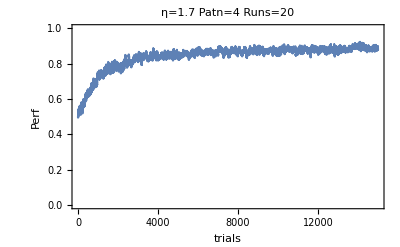

```mathematica
PlotPerfInFile[15000,eta,"OnlineRuleAMPA_XOR2_rate_HR40-5_Origin"]
```

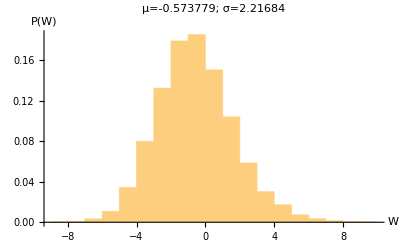

```mathematica
PlotWeightsInFile[15000,eta,"OnlineRuleAMPA_XOR2_rate_HR40-5_Origin"]
```

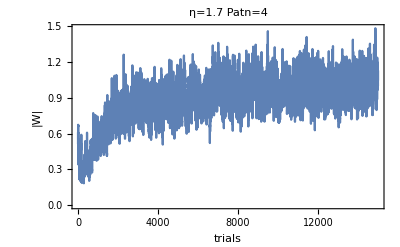

```mathematica
PlotWEvolInFile[15000,eta,"OnlineRuleAMPA_XOR2_rate_HR40-5_Origin",0.2]
```

```mathematica
StatActXorInFilePreLearning[15000,eta,"OnlineRuleAMPA_NMDASTDP10_XOR2_Origin"]
```

```mathematica
StatActXorInFile2[15000,eta,"OnlineRuleAMPA_XOR2_rate_HR40-5_Origin"]
```

{0.,0.95,0.65,0.05}

{0.1,0.95,0.7,0.05}

{0.1,0.9,0.85,0.}

{0.05,0.95,1.,0.1}

{0.05,1.,0.95,0.}

{0.05,0.95,0.9,0.}

{0.,0.85,1.,0.}

{0.05,0.75,0.95,0.05}

{0.05,0.95,0.95,0.}

{0.05,1.,1.,0.1}

{0.93375,{0.05,0.925,0.895,0.035}}

### R-STDP(dendritic spikes-PSPs)

#### code

```mathematica
{Ap,An,τp,τn}={0.188,0(*-0.094/2*),10.,20.};(* constants for STDP *)
```

```mathematica
stepper =
InlComp[
{mempots,spikegenNMDA,incrBuff,myUnitStep,ϕN,ϕS,k2,DϕN,DlϕN,DϕS,DlϕS,Tonl,step,stNMDA,tNMDA,Urest,β2,tmrsfac,tmrini,αg,βg,γg,αl,βl,γl,UmaxSoma,τfrac,Ap,An,τp,τn,τs,τm,spikegenPreSyn},
{{myinps,_Real,1},   (* input rates *)
{myw,_Real,2},(* weights for the "dendritic neurons" and AMPA synapses for the first component*)
{resets,_Integer,1}, (* the NMDA spike response *)
{reset,_Real}, (* the reset kernel for the soma *)
{ETr,_Real,2}, (* the eligibility trace *)
{APBuff,_Real,1}, (* mmemory of the AP *)
{PSPBuff,_Real,1} (* memory of the pre-synaptic spikes *)
},
Block[ {uSoma (*membrane potential at the soma *),ud, ntUpd,thisinp,spikesNMDA,SpikeSoma,us,nw,i,len,istepperlist,mask,nmyresets,nmyreset,nBufUpd ,inRefPer,nUspikeNMDA,κ,ntNMDASpBuff,EligSoma,ntPSPBuff,intRefdendStruct,myET,indBuff=0,NMDASpikeCounts,θMultSpike=(1.15),nmBuffSyn,uTmp,DendStruct,nmyinps,naAMPA,PSPm,PSPs,spikesPre},

(*local compy to change of context only at the begining*)
nmyinps=myinps;
PSPm=0.0*nmyinps;
PSPs=0.0*nmyinps;
spikesPre=PSPs;
mask = Mask;
naAMPA=aAMPA;
nUspikeNMDA=UspikeNMDA;
κ=N[k2*(Exp[β2*nUspikeNMDA]-1.)];
len = Round[Tonl/step];
istepperlist = stepperlist;
myET=(*0.0**)ETr;
nw = myw;
nmyresets =(*0.0**)resets (*Table[0,{Length@nw}]*);
intRefdendStruct= nmyresets*0-stNMDA;
inRefPer=Table[0.,{Length@nw}];
DendStruct=Table[{1.},{Length@nw}];
NMDASpikeCounts=inRefPer;
EligSoma=inRefPer;
nmyreset=(*0.**)reset;
ntNMDASpBuff=(*0.0**)APBuff(*Updinc*);(* memory of the state of the synapses when a NMDA spike occurs*)
(*represent the 50ms low pass filter of the no spiking part of Pfister ET*)
(*nBufUpd = PSPBuff*)(* Table[ntUpd,{stNMDA}]*);(* buffer for e^iv *)
ntPSPBuff=PSPBuff; 
ntUpd=0.0*nw;
uSoma=0.;
EligSoma=inRefPer;
uTmp=inRefPer;


For[i=1, i≤len,i++,
(*indBuff=incrBuff[indBuff];*)
nmyresets = nmyresets+1; (* refractoriness period *)
inRefPer=0.5(Sign[nmyresets-0.1] +1.) ;(* determine the sign of the  attenuation integral *)

spikesPre=spikegenPreSyn[nmyinps];
PSPm=spikesPre+(1.0-step/τm)PSPm;
PSPs=spikesPre+(1.0-step/τs)PSPs;
thisinp ={(PSPm-PSPs)/(τm-τs)};   (* vector of inputs as a matrix *)


ud= mempots[nw,thisinp] ; (* calculate the membrane potential in the dendritic branchs ("line vector") *)
spikesNMDA= spikegenNMDA[ud(*,inRefPer*)]; (* calculate the NMDA spikes *)
uSoma=nUspikeNMDA*Total[1.-inRefPer]-nmyreset+Urest+naAMPA*Total[Flatten@ud-Urest];
nmyreset = nmyreset  tmrsfac;
NMDASpikeCounts=NMDASpikeCounts*(1.0-step/tNMDA);

SpikeSoma=0.5+0.5*Sign[1-Exp[-(step * ϕS[uSoma])]-RandomReal[{0,1}]];
(* somatic spike *)
If[SpikeSoma==1.0,
nmyreset+=tmrini;
Sow[ i];
];
spikesPre;

ntNMDASpBuff=(1.0-step/τn)ntNMDASpBuff;
ntPSPBuff=Ap/τp*spikesPre+(1.0-step/τp)ntPSPBuff;
ntUpd=0.ntUpd;
(* NMDA spikes *)
If [spikesNMDA ≠ {0} ,(
ntUpd[[spikesNMDA ]]  =DendStruct[[spikesNMDA ]] .{ntPSPBuff};
ntNMDASpBuff[[spikesNMDA ]] +=An/τn;
nmyresets[[spikesNMDA ]] = intRefdendStruct[[spikesNMDA ]];
Sow[ i,spikesNMDA];
us = ud[[spikesNMDA]];
)];

ntUpd +=((DendStruct ntNMDASpBuff).{spikesPre});
myET=ntUpd+(1.0-step/(τfrac*Tonl))myET;

If[(istepperlist==1 ),
Sow[{uSoma,ud},"ReturnValue"];
];

];
Sow[{uSoma,ud},"ReturnValue"];
Sow[{nw,nmyresets,nmyreset,myET,ntNMDASpBuff,ntPSPBuff},"ReturnValue"];
],
{{Mask,_Real,2},{UspikeNMDA,_Real},{stepperlist,_Integer},{aAMPA,_Real},{Position[_, 1],_Integer,2}}
];
```

#### simulation

```mathematica
eta=1.5;
```

```mathematica
iter=15000;
```

```mathematica
Table[Print@Timing@learnInFile[iter,0,eta,"OnlineRuleAMPA_NMDASTDP10_XOR2_Origin"],{10}];
```

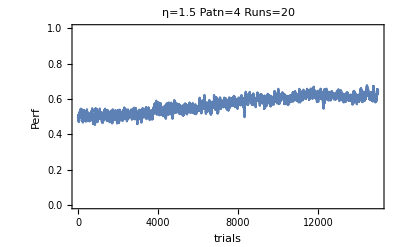

```mathematica
PlotPerfInFile[iter,eta,"OnlineRuleAMPA_NMDASTDP10_XOR2_Origin"]
```

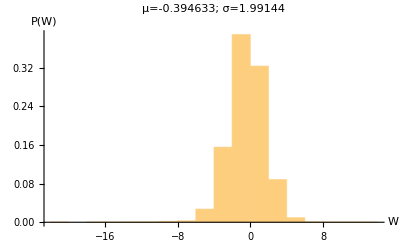

```mathematica
PlotWeightsInFile[iter,eta,"OnlineRuleAMPA_NMDASTDP10_XOR2_Origin"]
```

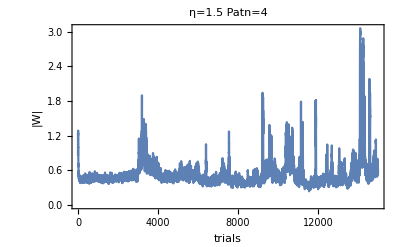

```mathematica
PlotWEvolInFile[iter,eta,"OnlineRuleAMPA_NMDASTDP10_XOR2_Origin",0.2]
```

```mathematica
StatActXorInFilePreLearning[iter,eta,"OnlineRuleAMPA_NMDASTDP10_XOR2_Origin"]
```

Mean activity ((00),(10),(01),(11))

{21.9615,27.2586,21.9111,23.9111}

{1.,1.,1.,1.}

```mathematica
StatActXorInFile2[iter,eta,"OnlineRuleAMPA_NMDASTDP10_XOR2_Origin"]
```

{1.,1.,1.,0.25}

{0.35,0.8,0.65,0.45}

{0.4,0.6,0.5,0.25}

{0.5,0.7,0.75,0.35}

{1.,1.,1.,0.8}

{0.4,1.,0.7,1.}

{0.,0.15,0.3,0.1}

{0.65,0.8,0.3,0.4}

{0.3,0.95,0.85,1.}

{1.,0.95,0.95,0.4}

{1.,1.,0.95,0.45}

{0.1,1.,0.95,1.}

{1.,0.85,1.,0.15}

{0.45,0.85,0.7,0.65}

{0.2,0.95,1.,1.}

{0.15,1.,0.75,1.}

{0.35,0.65,0.6,0.45}

{1.,0.7,0.9,0.3}

{1.,1.,0.9,0.35}

{0.2,0.9,0.4,0.2}

{0.63,{0.5525,0.8425,0.7575,0.5275}}

```mathematica
OptPadding={{42,26},{29,9}};
```

```mathematica
(*exp. moving average *)
 λFilter[incs_,λ_] := Block[ {fm},
fm[s_,inc_] := (1-λ)s + λ inc; 
FoldList[fm,0.5,incs]//Rest
];
```

```mathematica
StatActXorInFilePreLearning2[fileN_]:=Block[{tmp,tmp2,res,wwin,Seedtab,WTab,k,x1,x2,last,Y,Z,nbSample=20,totalRuns},
res=ReadList[fileN];
totalRuns=Length@res;
WTab=res/.trialDT[_,_,_,_,outDT[a_],_,_]->a;
Seedtab=res/.trialDT[_,_,_,_,_,outDT[a_],_]->a;

res=Transpose@Table[
SeedRandom[Seedtab[[k]]];
{wwin,Mask} = myiniws[0,σW,nbNeuron,pConnect];
Patn=4;

Table[
{x1,x2}=getXid[ p];(* choose ramndom pattern *)
Table[
{last,{Y,Z}}=nextpassEpisode[Patsepsps[x1,x2],ini[(*tmp*)wwin]];
(*1-Abs[Sign@Length@Flatten@Z-Mod[x1+x2,2]]*)
Abs[(1.-Sign[x1+x2])-Sign@Length@Flatten@Z]
,{nbSample}]
,{p,Patn}]
,{k,totalRuns}];
{{N@Mean@Flatten[res],N@StandardDeviation@Flatten[res]/Sqrt[Patn totalRuns-1]},Map[{N@Mean@Flatten[#],N@StandardDeviation@Flatten[#]/Sqrt[totalRuns-1]}&,res]}
];
```

```mathematica
{PerfIni,PerfsIni}=StatActXorInFilePreLearning2[getFileName[1.5,15000,"OnlineRuleAMPA_NMDASTDP10_XOR2_Origin"]]
```

{{0.75,0.048733},{{0.,0.},{1.,0.},{1.,0.},{1.,0.}}}

```mathematica
FileNameOR2=getFileName[1.5,15000,"OnlineRuleAMPA_NMDASTDP10_XOR2_Origin"];
```

```mathematica
rest=ReadList[FileNameOR2];
```

```mathematica
rest=Take[rest,20];
```

```mathematica
PerfGlob=rest/.trialDT[outDT[a_],_,_,_,_,_,_]->a;
```

```mathematica
PerfGlob=Map[λFilter[1#,0.2/Patn]&,PerfGlob];
```

```mathematica
GlobRange={1}~Join~Range[1360,14800,1500]~Join~{15000};
```

```mathematica
ErrorPtsGlobSTDPNMDA=(*{{{1,PerfIni[[1]]},ErrorBar[PerfIni[[2]]]}}~Join~*)MapThread[{{#3,#1},ErrorBar[#2]}&,{(Mean@PerfGlob)[[GlobRange]],(StandardDeviation@PerfGlob/Sqrt[Length@PerfGlob-1])[[GlobRange]],GlobRange}]
```

{{{1,0.4975},ErrorBar[0.00585489]},{{1360,0.524348},ErrorBar[0.0186325]},{{2860,0.514417},ErrorBar[0.0202158]},{{4360,0.508984},ErrorBar[0.0144631]},{{5860,0.558255},ErrorBar[0.0177835]},{{7360,0.579189},ErrorBar[0.0265818]},{{8860,0.592786},ErrorBar[0.0274523]},{{10360,0.589669},ErrorBar[0.0235868]},{{11860,0.606593},ErrorBar[0.0208231]},{{13360,0.62008},ErrorBar[0.0179048]},{{15000,0.644173},ErrorBar[0.0263636]}}

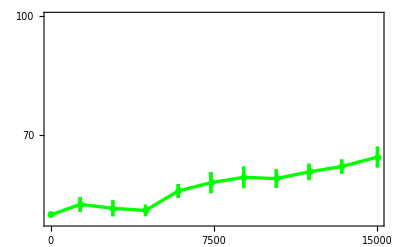

```mathematica
PlotPerfOR2=ErrorListPlot[{ErrorPtsGlobSTDPNMDA},Joined->True,Frame->True,Axes->False,ImageSize->400,FrameTicks->{ {0,7500,15000},{  {0.4,40},{0.7,70},{1.0,100}}, None, None},BaseStyle->18,LabelStyle->(FontFamily->"Helvetica"),(*FrameLabel->{"trials","Performance (%)"},*)PlotRange->{0.48,1},PlotStyle->{{Green,Thickness[0.006]}},PlotMarkers->Automatic,ImagePadding->OptPadding]
```

### R - STDP (APs - PSPs)

#### code

```mathematica
{Ap,An,τp,τn}={0.188,0(*-0.094/2*),10.,20.};(* constants for STDP *)
```

```mathematica
stepper =
InlComp[
{mempots,spikegenNMDA,incrBuff,myUnitStep,ϕN,ϕS,k2,DϕN,DlϕN,DϕS,DlϕS,Tonl,step,stNMDA,tNMDA,Urest,β2,tmrsfac,tmrini,αg,βg,γg,αl,βl,γl,UmaxSoma,τfrac,τInhib,Ap,An,τp,τn,τs,τm,spikegenPreSyn},
{{myinps,_Real,1},   (* input rates *)
{myw,_Real,2},(* weights for the "dendritic neurons" and AMPA synapses for the first component*)
{resets,_Integer,1}, (* the NMDA spike response *)
{reset,_Real}, (* the reset kernel for the soma *)
{ETr,_Real,2}, (* the eligibility trace *)
{APBuff,_Real}, (* mmemory of the AP *)
{PSPBuff,_Real,1} (* memory of the pre-synaptic spikes *)
},
Block[ {uSoma (*membrane potential at the soma *),ud, ntUpd,thisinp,spikesNMDA,SpikeSoma,us,nw,i,len,istepperlist,mask,nmyresets,nmyreset,nBufUpd ,inRefPer,nUspikeNMDA,κ,ntAPBuff,EligSoma,ntPSPBuff,intRefdendStruct,myET,indBuff=0,NMDASpikeCounts,θMultSpike=(1.15),nmBuffSyn,uTmp,DendStruct,nmyinps,naAMPA,PSPm,PSPs,spikesPre},

(*local compy to change of context only at the begining*)
nmyinps=myinps;
PSPm=0.0*nmyinps;
PSPs=0.0*nmyinps;
spikesPre=PSPs;
mask = Mask;
naAMPA=aAMPA;
nUspikeNMDA=UspikeNMDA;
κ=N[k2*(Exp[β2*nUspikeNMDA]-1.)];
len = Round[Tonl/step];
istepperlist = stepperlist;
myET=(*0.0**)ETr;
nw = myw;
nmyresets =(*0.0**)resets (*Table[0,{Length@nw}]*);
intRefdendStruct= nmyresets*0-stNMDA;
inRefPer=Table[0.,{Length@nw}];
DendStruct=Table[{1.},{Length@nw}];
NMDASpikeCounts=inRefPer;
EligSoma=inRefPer;
nmyreset=(*0.**)reset;
ntAPBuff=(*0.0**)APBuff(*Updinc*);(* memory of the state of the synapses when a NMDA spike occurs*)
(*represent the 50ms low pass filter of the no spiking part of Pfister ET*)
(*nBufUpd = PSPBuff*)(* Table[ntUpd,{stNMDA}]*);(* buffer for e^iv *)
ntPSPBuff=PSPBuff; 
ntUpd=0.0*ntPSPBuff;
uSoma=0.;
EligSoma=inRefPer;
uTmp=inRefPer;


For[i=1, i≤len,i++,
(*indBuff=incrBuff[indBuff];*)
nmyresets = nmyresets+1; (* refractoriness period *)
inRefPer=0.5(Sign[nmyresets-0.1] +1.) ;(* determine the sign of the  attenuation integral *)

spikesPre=spikegenPreSyn[nmyinps];
PSPm=spikesPre+(1.0-step/τm)PSPm;
PSPs=spikesPre+(1.0-step/τs)PSPs;
thisinp ={(PSPm-PSPs)/(τm-τs)};   (* vector of inputs as a matrix *)


ud= mempots[nw,thisinp] ; (* calculate the membrane potential in the dendritic branchs ("line vector") *)
spikesNMDA= spikegenNMDA[ud(*,inRefPer*)]; (* calculate the NMDA spikes *)
uSoma=nUspikeNMDA*Total[1.-inRefPer]-nmyreset+Urest+naAMPA*Total[Flatten@ud-Urest];
nmyreset = nmyreset  tmrsfac;
NMDASpikeCounts=NMDASpikeCounts*(1.0-step/tNMDA);

SpikeSoma=0.5+0.5*Sign[1-Exp[-(step * ϕS[uSoma])]-RandomReal[{0,1}]];
(* somatic spike *)
If[SpikeSoma==1.0,
nmyreset+=tmrini;
Sow[ i];
];
ntAPBuff=An/τn SpikeSoma+(1.0-step/τn)ntAPBuff;
ntPSPBuff=Ap/τp*spikesPre+(1.0-step/τp)ntPSPBuff;

ntUpd =(spikesPre*ntAPBuff)+(SpikeSoma*ntPSPBuff);


(* NMDA spikes *)
If [spikesNMDA ≠ {0} ,(
nmyresets[[spikesNMDA ]] = intRefdendStruct[[spikesNMDA ]];
Sow[ i,spikesNMDA];
us = ud[[spikesNMDA]];
)];

myET=(DendStruct.{ntUpd})+(1.0-step/(τfrac*Tonl))myET;

If[(istepperlist==1 ),
Sow[{uSoma,ud},"ReturnValue"];
];

];
Sow[{uSoma,ud},"ReturnValue"];
Sow[{nw,nmyresets,nmyreset,myET,ntAPBuff,ntPSPBuff},"ReturnValue"];
],
{{Mask,_Real,2},{UspikeNMDA,_Real},{stepperlist,_Integer},{aAMPA,_Real},{Position[_, 1],_Integer,2}}
];
```

#### simulation

```mathematica
eta=4.5;
```

```mathematica
iter=15000;
```

```mathematica
Table[Print@Timing@learnInFile[iter,0,eta,"OnlineRuleAMPA_STDP10_XOR2_Origin"],{20}];
```

seed=3565274477

{1499.75,Null}

seed=3565275976

{1466.62,Null}

seed=3565277443

{1472.32,Null}

seed=3565278915

{1470.29,Null}

seed=3565280385

{1538.36,Null}

seed=3565281924

{1470.5,Null}

seed=3565283394

{1478.78,Null}

seed=3565284873

{1547.46,Null}

seed=3565286420

{1477.58,Null}

seed=3565287898

{1463.26,Null}

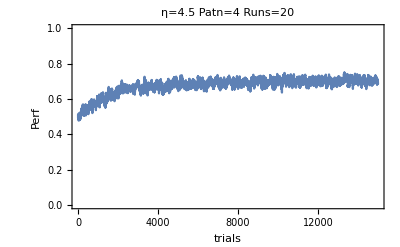

```mathematica
PlotPerfInFile[iter,eta,"OnlineRuleAMPA_STDP10_XOR2_Origin"]
```

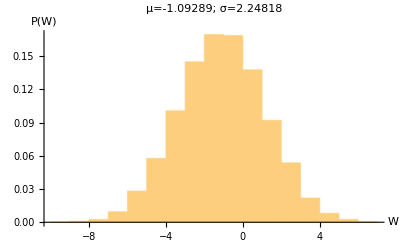

```mathematica
PlotWeightsInFile[iter,eta,"OnlineRuleAMPA_STDP10_XOR2_Origin"]
```

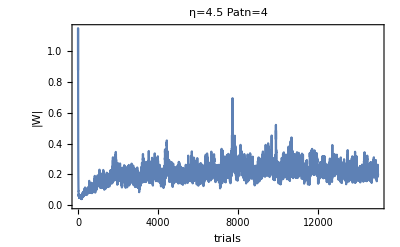

```mathematica
PlotWEvolInFile[iter,eta,"OnlineRuleAMPA_STDP10_XOR2_Origin",0.2]
```

```mathematica
StatActXorInFilePreLearning[iter,eta,"OnlineRuleAMPA_STDP10_XOR2_Origin"]
```

Mean activity ((00),(10),(01),(11))

{12.7826,13.0408,13.7358,12.7885}

{0.804348,0.734694,0.792453,0.807692}

```mathematica
StatActXorInFile2[iter,eta,"OnlineRuleAMPA_STDP10_XOR2_Origin"]
```

{0.15,0.05,0.25,0.}

{0.,0.,0.15,0.05}

{0.05,0.05,0.05,0.}

{0.,0.05,0.,0.}

{0.,0.05,0.05,0.}

{0.55,0.15,0.,0.}

{0.05,0.,0.05,0.}

{0.1,0.,0.,0.}

{0.,0.15,0.05,0.}

{0.05,0.,0.25,0.05}

{0.,0.15,0.,0.1}

{0.05,0.1,0.05,0.}

{0.,0.,0.15,0.}

{0.,0.,0.1,0.}

{0.2,0.05,0.25,0.05}

{0.,0.15,0.05,0.05}

{0.,0.2,0.,0.05}

{0.1,0.05,0.,0.05}

{0.,0.05,0.25,0.}

{0.05,0.2,0.05,0.05}

{0.5175,{0.0675,0.0725,0.0875,0.0225}}

```mathematica
FileNameXOR2=getFileName[eta,iter,"OnlineRuleAMPA_STDP10_XOR2_Origin"];
```

```mathematica
rest=ReadList[FileNameXOR2];
```

```mathematica
rest=Take[rest,20];
```

```mathematica
PerfGlob=rest/.trialDT[outDT[a_],_,_,_,_,_,_]->a;
```

```mathematica
PerfGlob=Map[λFilter[1.#,0.2/Patn]&,PerfGlob];
```

```mathematica
GlobRange={1}~Join~Range[1400,14500,1500]~Join~{14980};
```

```mathematica
ErrorPtsGlobSTDP=(*{{{1,PerfIni[[1]]},ErrorBar[PerfIni[[2]]]}}~Join~*)MapThread[{{#3,#1},ErrorBar[#2]}&,{(Mean@PerfGlob)[[GlobRange]],(StandardDeviation@PerfGlob/Sqrt[Length@PerfGlob-1])[[GlobRange]],GlobRange}]
```

{{{1,0.4625},ErrorBar[0.00509603]},{{1400,-0.365657},ErrorBar[0.0137508]},{{2900,-0.317493},ErrorBar[0.0217601]},{{4400,-0.321611},ErrorBar[0.0200574]},{{5900,-0.325004},ErrorBar[0.0180495]},{{7400,-0.327464},ErrorBar[0.0190324]},{{8900,-0.302364},ErrorBar[0.0167057]},{{10400,-0.318437},ErrorBar[0.0195894]},{{11900,-0.30622},ErrorBar[0.0170947]},{{13400,-0.292916},ErrorBar[0.0180649]},{{14980,-0.294133},ErrorBar[0.0205875]}}

### Comparison

```mathematica
aAMPA=0;
```

```mathematica
OptPadding={{40,27},{28,6}};
```

```mathematica
(*exp. moving average *)
 λFilter[incs_,λ_] := Block[ {fm},
fm[s_,inc_] := (1-λ)s + λ inc; 
FoldList[fm,0.5,incs]//Rest
];
```

```mathematica
StatActXorInFilePreLearning2[fileN_]:=Block[{tmp,tmp2,res,wwin,Seedtab,WTab,k,x1,x2,last,Y,Z,nbSample=20,totalRuns},
res=ReadList[fileN];
totalRuns=Length@res;
WTab=res/.trialDT[_,_,_,_,outDT[a_],_,_]->a;
Seedtab=res/.trialDT[_,_,_,_,_,outDT[a_],_]->a;

res=Transpose@Table[
SeedRandom[Seedtab[[k]]];
{wwin,Mask} = myiniws[0,σW,nbNeuron,pConnect];
Patn=4;

Table[
{x1,x2}=getXid[ p];(* choose ramndom pattern *)
Table[
{last,{Y,Z}}=nextpassEpisode[Patsepsps[x1,x2],ini[(*tmp*)wwin]];
(*1-Abs[Sign@Length@Flatten@Z-Mod[x1+x2,2]]*)
Abs[(1.-Sign[x1+x2])-Sign@Length@Flatten@Z]
,{nbSample}]
,{p,Patn}]
,{k,totalRuns}];
{{N@Mean@Flatten[res],N@StandardDeviation@Flatten[res]/Sqrt[Patn totalRuns-1]},Map[{N@Mean@Flatten[#],N@StandardDeviation@Flatten[#]/Sqrt[totalRuns-1]}&,res]}
];
```

```mathematica
OptPadding={{42,26},{29,9}};
```

```mathematica
{PerfIni,PerfsIni}=StatActXorInFilePreLearning2[getFileName[2.66,15000,"OnlineRuleAMPA_XOR2_rate_HR40-5_Origin"]]
```

$Aborted

```mathematica
FileNameXOR2=getFileName[2.66,15000,"OnlineRuleAMPA_XOR2_rate_HR40-5_Origin"];
```

```mathematica
rest=ReadList[FileNameXOR2];
```

```mathematica
rest=Take[rest,20];
```

```mathematica
PerfGlob=rest/.trialDT[outDT[a_],_,_,_,_,_,_]->a;
```

```mathematica
PerfGlob=Map[λFilter[1.+#,0.2/Patn]&,PerfGlob];
```

```mathematica
GlobRange={1}~Join~Range[1540,14800,1500]~Join~{15000};
```

```mathematica
ErrorPtsGlob=(*{{{1,PerfIni[[1]]},ErrorBar[PerfIni[[2]]]}}~Join~*)MapThread[{{#3,#1},ErrorBar[#2]}&,{(Mean@PerfGlob)[[GlobRange]],(StandardDeviation@PerfGlob/Sqrt[Length@PerfGlob-1])[[GlobRange]],GlobRange}];
```

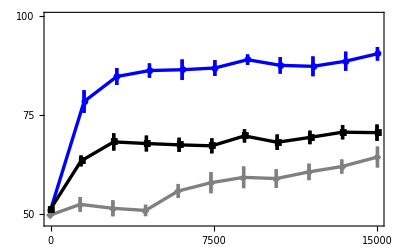

```mathematica
OptPadding={{40,27},{28,8}};PlotPerfXOR2=ErrorListPlot[{ErrorPtsGlob,ErrorPtsGlobSTDP,ErrorPtsGlobSTDPNMDA},Joined->True,Frame->{{True,True},{True,False}},Axes->False,ImageSize->400,FrameTicks->{ {0,7500,15000},{  {0.5,50},{0.75,75},{1.,100}}, None, None},BaseStyle->22,LabelStyle->(FontFamily->"Helvetica"),(*FrameLabel->{"trials","Performance (%)"},*)PlotRange->{0.48,1},PlotStyle->{{Blue,Thickness[0.006]},{Black,Thickness[0.006]},{Gray,Thickness[0.006]}},PlotMarkers->Automatic,ImagePadding->OptPadding]
```

```mathematica
Export["PlotPerfXOR2.png",PlotPerfXOR2]
```

PlotPerfXOR2.png

#### plot perf best η

```mathematica
aAMPA=0;
```

```mathematica
DataPerf=StatActXorInFile2Data[15000,2.66,"OnlineRuleAMPA_XOR2_rate_HR40-5_Origin"];
```

```mathematica
DataPerfm=Map[100Mean@Abs[{1,0,0,1}-Mean[#]]&,N@DataPerf]
```

{88.75,87.5,91.25,95.,97.5,95.,96.25,90.,96.25,96.25,97.5,95.,93.75,93.75,88.75,91.25,77.5,93.75,75.,66.25}

```mathematica
OptPadding={{42,26},{22,9}};
```

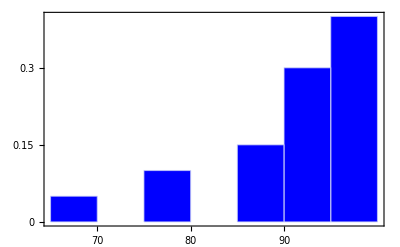

```mathematica
Histogram[DataPerfm,{5},"Probability",(*FrameLabel->{"Perf (%)","P(Perf)"},*)BaseStyle->18,LabelStyle->(FontFamily->"Helvetica"),ChartStyle->{Blue(*,Directive[Magenta,EdgeForm[Dashed]]*)},Axes->False,ImageSize->400,Frame->{{True,False},{True,False}},FrameTicks->{{{0,0.15,0.3},None},{{70,80,90},None}},ImageSize->400,PlotRange->All,PlotRangePadding->{{4,1},{0,0.03}}]
```

```mathematica
DataPerfmSTDPNMDA=StatActXorInFile2Data[15000,1.5,"OnlineRuleAMPA_NMDASTDP10_XOR2_Origin"];
```

```mathematica
DataPerfmSTDP=StatActXorInFile2Data[15000,1.7,"OnlineRuleAMPA_XOR2_rate_HR40-5_Origin"];
```

```mathematica
histDataPerfm=HistogramList[DataPerfm,{50,100,10},"Probability"];
```

```mathematica
histDataPerfmSTDP=HistogramList[DataPerfmSTDP,{50,100,10},"Probability"];
```

```mathematica
histDataPerfmSTDPNMDA=HistogramList[DataPerfmSTDPNMDA,{50,100,10},"Probability"];
```

```mathematica
histDataPerfm
```

{{50,60,70,80,90,100},{0.,0.05,0.1,0.15,0.7}}

```mathematica
histDataPerfmSTDP
```

{{50,60,70,80,90,100},{0.,0.2,0.8,0.,0.}}

```mathematica
labelsChart=Map[ToString[#]<>"-"<>ToString[#+10]&,First@histDataPerfm]
```

{50-60,60-70,70-80,80-90,90-100,100-110}

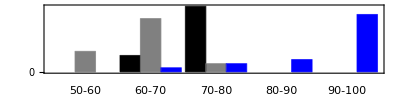

```mathematica
PlotPerfXORHist=BarChart[Transpose[{Last@histDataPerfmSTDP,Last@histDataPerfmSTDPNMDA,Last@histDataPerfm}],ChartStyle->{Black,Gray,Blue},ChartLabels->{labelsChart(*Placed[labelsChart,{0.4,-0.2}]*),None},BaseStyle->{22,Thickness[0.01]},Frame->{{True,False},{True,False}},FrameTicks->{{{0,0.5,1},None},{{60,70,80,90,100},None}},PlotRangePadding->{{-0.08,0},{0.00,0}},BarSpacing->0,AspectRatio->0.25,ImageSize->400]
```

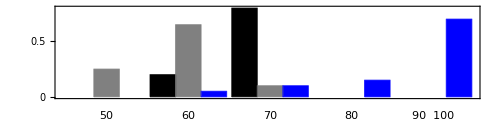

```mathematica
PlotPerfXORHist=BarChart[Transpose[{Last@histDataPerfmSTDP,Last@histDataPerfmSTDPNMDA,Last@histDataPerfm}],ChartStyle->{Black,Gray,Blue},ChartLabels->{{"50          ","60          ","70          ","80          ","90  100"}(*Placed[labelsChart,{0.4,-0.2}]*),None},BaseStyle->{36,Thickness[0.01]},Frame->{{True,False},{True,False}},FrameTicks->{{{0,0.5,1},None},{{60,70,80,90,100},None}},PlotRangePadding->{{-0,0},{0.00,0}},BarSpacing->0,AspectRatio->0.25,ImageSize->500]
```

```mathematica
Export["PlotPerfXORHist.png",PlotPerfXORHist,ImageResolution->600]
```

PlotPerfXORHist.png